```mathematica
Needs["OGRe`"]
```

OGRe: An Object-Oriented General Relativity Package for Mathematica
By Barak Shoshany ([baraksh@gmail.com](mailto:baraksh@gmail.com)) ([baraksh.com](https://baraksh.com/))
v1.7.0 (2021-09-17)
GitHub repository: https://github.com/bshoshany/OGRe
• To view the full documentation for the package, type .
• To list all available modules, type .
• To get help on a particular module, type ? followed by the module name.
• To enable parallelization, type .
•  To disable automatic checks for updates at startup, type .

```mathematica
?OGRe`*
```

```mathematica
TNewCoordinates["Cartesian",{t,x,y,z}]
```

Cartesian

```mathematica
TSetReservedSymbols[{a}];
TShow@TNewMetric["flatFLRW","Cartesian",DiagonalMatrix[{-a[t]^2,a[t]^2,a[t]^2 ,a[t]^2 }]]
```

flatFLRW:   g_μν^μν(,,txyz) = (-a^2 | 0 | 0 | 0
0 | a^2 | 0 | 0
0 | 0 | a^2 | 0
0 | 0 | 0 | a^2)

```mathematica
(* Assume aniosotropy, choose x-axis without loss of generalization *)
TNewTensor["Phi","flatFLRW","Cartesian",{},{φ[t,x,y,z]},"φ"]
TShow@TNewTensor["PhiVec","flatFLRW","Cartesian",{-1},{φt[t,x,y,z],φx[t,x,y,z],φy[t,x,y,z],φz[t,x,y,z]},"φ"]
TShow@TNewTensor["PhiMat","flatFLRW","Cartesian",{-1,-1},{{0,φtx[t,x,y,z],φty[t,x,y,z],φtz[t,x,y,z]}, {-φtx[t,x,y,z],0,φxy[t,x,y,z],φxz[t,x,y,z]},{-φty[t,x,y,z],-φxy[t,x,y,z],0,φyz[t,x,y,z]},{-φtz[t,x,y,z],-φxz[t,x,y,z],-φyz[t,x,y,z],0}},"φ"]
TNewTensor["Psi","flatFLRW","Cartesian",{},{ψ[t,x,y,z]},"ψ"]
TShow@TNewTensor["PsiVec","flatFLRW","Cartesian",{-1},{ψt[t,x,y,z],ψx[t,x,y,z],ψy[t,x,y,z],ψz[t,x,y,z]},"ψ"]
TNewTensor["Eps4D","flatFLRW","Cartesian",{1,1,1,1},Normal[LeviCivitaTensor[4]]]
```

Phi

PhiVec:   φ_μ^μ(,,txyz) = (φt[t,x,y,z]
φx[t,x,y,z]
φy[t,x,y,z]
φz[t,x,y,z])

PhiMat:   φ_μν^μν(,,txyz) = (0 | φtx[t,x,y,z] | φty[t,x,y,z] | φtz[t,x,y,z]
-φtx[t,x,y,z] | 0 | φxy[t,x,y,z] | φxz[t,x,y,z]
-φty[t,x,y,z] | -φxy[t,x,y,z] | 0 | φyz[t,x,y,z]
-φtz[t,x,y,z] | -φxz[t,x,y,z] | -φyz[t,x,y,z] | 0)

Psi

PsiVec:   ψ_μ^μ(,,txyz) = (ψt[t,x,y,z]
ψx[t,x,y,z]
ψy[t,x,y,z]
ψz[t,x,y,z])

Eps4D

## Kahler Dirac equation with first derivative

```mathematica
TList@TSimplify@TCalc["Eq1",TCovariantD["μ"]."PhiVec"["μ"]-m "Phi"[""]]
```

TMessage::ErrorDoesNotExist: The tensor "_TCalcTemp1_" does not exist.

$Aborted

```mathematica
(* Define Kahler Dirac equations *)
(* Equation 1 *)
TList@TSimplify@TCalc["Eq1",TCovariantD["μ"]."PhiVec"["μ"]-m "Phi"[""]]
(* Equation 2 *)
TList@TSimplify@TCalc["Eq2",TCovariantD["μ"]."Phi"[""]+TCovariantD["ν"]."PhiMat"["νμ"]-m "PhiVec"["μ"]]
(* Equation 3 *)
TList@TSimplify@TCalc[ "Eq3",TCovariantD["μ"]."PhiVec"["ν"]-TCovariantD["ν"]."PhiVec"["μ"]+ TCovariantD["α"]."PsiVec"["β"]."Eps4D"["αβμν"]-m "PhiMat"["μν"]]
(* Equation 4 *)
TList@TSimplify@TCalc["Eq4",1/2  "Eps4D"["μαβν"].TCovariantD["μ"]."PhiMat"["αβ"]+TCovariantD["ν"]."Psi"[""]-m "PsiVec"["ν"]]
(* Equation 5 *)
TList@TSimplify@TCalc["Eq5",TCovariantD["μ"]."PsiVec"["μ"]-m "Psi"[""]]
```

Eq1:
==⬚_^ | = | -m φ[t,x,y,z]+(-2 φt[t,x,y,z] Inactiveat+a (-Inactiveφt[t,x,y,z]t+Inactiveφx[t,x,y,z]x+Inactiveφy[t,x,y,z]y+Inactiveφz[t,x,y,z]z))/a^3

Eq2:
==⬚_t^t | = | -m φt[t,x,y,z]+Inactiveφ[t,x,y,z]t-(Inactiveφtx[t,x,y,z]x+Inactiveφty[t,x,y,z]y+Inactiveφtz[t,x,y,z]z)/a^2
==⬚_x^x | = | -m φx[t,x,y,z]+Inactiveφ[t,x,y,z]x-(Inactiveφtx[t,x,y,z]t+Inactiveφxy[t,x,y,z]y+Inactiveφxz[t,x,y,z]z)/a^2
==⬚_y^y | = | -m φy[t,x,y,z]+Inactiveφ[t,x,y,z]y-(Inactiveφty[t,x,y,z]t-Inactiveφxy[t,x,y,z]x+Inactiveφyz[t,x,y,z]z)/a^2
==⬚_z^z | = | -m φz[t,x,y,z]+Inactiveφ[t,x,y,z]z+(-Inactiveφtz[t,x,y,z]t+Inactiveφxz[t,x,y,z]x+Inactiveφyz[t,x,y,z]y)/a^2

Eq3:
==⬚_tx^tx-⬚_xt^xt | = | (m φtx[t,x,y,z]+Inactiveφt[t,x,y,z]x-Inactiveφx[t,x,y,z]t)/a^4-Inactiveψy[t,x,y,z]z+Inactiveψz[t,x,y,z]y
==⬚_ty^ty-⬚_yt^yt | = | (m φty[t,x,y,z]+Inactiveφt[t,x,y,z]y-Inactiveφy[t,x,y,z]t)/a^4+Inactiveψx[t,x,y,z]z-Inactiveψz[t,x,y,z]x
==⬚_tz^tz-⬚_zt^zt | = | (m φtz[t,x,y,z]+Inactiveφt[t,x,y,z]z-Inactiveφz[t,x,y,z]t)/a^4-Inactiveψx[t,x,y,z]y+Inactiveψy[t,x,y,z]x
==⬚_xy^xy | = | (-m φxy[t,x,y,z]+4 a^3 ψz[t,x,y,z] Inactiveat-Inactiveφx[t,x,y,z]y+Inactiveφy[t,x,y,z]x)/a^4-Inactiveψt[t,x,y,z]z+Inactiveψz[t,x,y,z]t
==⬚_xz^xz-⬚_zx^zx | = | -(m φxz[t,x,y,z]+4 a^3 ψy[t,x,y,z] Inactiveat+Inactiveφx[t,x,y,z]z-Inactiveφz[t,x,y,z]x)/a^4+Inactiveψt[t,x,y,z]y-Inactiveψy[t,x,y,z]t
==⬚_yx^yx | = | (m φxy[t,x,y,z]-4 a^3 ψz[t,x,y,z] Inactiveat+Inactiveφx[t,x,y,z]y-Inactiveφy[t,x,y,z]x)/a^4+Inactiveψt[t,x,y,z]z-Inactiveψz[t,x,y,z]t
==⬚_yz^yz | = | (-m φyz[t,x,y,z]+4 a^3 ψx[t,x,y,z] Inactiveat-Inactiveφy[t,x,y,z]z+Inactiveφz[t,x,y,z]y)/a^4-Inactiveψt[t,x,y,z]x+Inactiveψx[t,x,y,z]t
==⬚_zy^zy | = | (m φyz[t,x,y,z]-4 a^3 ψx[t,x,y,z] Inactiveat+Inactiveφy[t,x,y,z]z-Inactiveφz[t,x,y,z]y)/a^4+Inactiveψt[t,x,y,z]x-Inactiveψx[t,x,y,z]t

Eq4:
==⬚_t^t | = | -Inactiveφxy[t,x,y,z]z+Inactiveφxz[t,x,y,z]y-Inactiveφyz[t,x,y,z]x+(m ψt[t,x,y,z]-Inactiveψ[t,x,y,z]t)/a^2
==⬚_x^x | = | Inactiveφty[t,x,y,z]z-Inactiveφtz[t,x,y,z]y+Inactiveφyz[t,x,y,z]t+(-m ψx[t,x,y,z]+Inactiveψ[t,x,y,z]x)/a^2
==⬚_y^y | = | (-m ψy[t,x,y,z]-a^2 (Inactiveφtx[t,x,y,z]z-Inactiveφtz[t,x,y,z]x+Inactiveφxz[t,x,y,z]t)+Inactiveψ[t,x,y,z]y)/a^2
==⬚_z^z | = | Inactiveφtx[t,x,y,z]y-Inactiveφty[t,x,y,z]x+Inactiveφxy[t,x,y,z]t+(-m ψz[t,x,y,z]+Inactiveψ[t,x,y,z]z)/a^2

Eq5:
==⬚_^ | = | -m ψ[t,x,y,z]+(-2 ψt[t,x,y,z] Inactiveat+a (-Inactiveψt[t,x,y,z]t+Inactiveψx[t,x,y,z]x+Inactiveψy[t,x,y,z]y+Inactiveψz[t,x,y,z]z))/a^3

## Kahler Dirac equation with Laplacian formulation (second derivative)

```mathematica
(* First calculate Riemann tensor, Ricci tensor,and Ricci scalar*)
TList@TCalcRiemannTensor["flatFLRW"]
TList@TCalcRicciTensor["flatFLRW"]
TList@TCalcRicciScalar["flatFLRW"]
```

flatFLRWRiemann:
==R_txtx^txtxR_tyty^tytyR_tztz^tztzR_xttx^xttxR_ytty^yttyR_zttz^zttz | = | (-Inactiveat^2+a Inactiveat^2)/a^2
==R_txxt^txxtR_tyyt^tyytR_tzzt^tzztR_xtxt^xtxtR_ytyt^ytytR_ztzt^ztzt | = | (Inactiveat^2-a Inactiveat^2)/a^2
==R_xyxy^xyxyR_xzxz^xzxzR_yxyx^yxyxR_yzyz^yzyzR_zxzx^zxzxR_zyzy^zyzy-R_xyyx^xyyx-R_xzzx^xzzx-R_yxxy^yxxy-R_yzzy^yzzy-R_zxxz^zxxz-R_zyyz^zyyz | = | Inactiveat^2/a^2

flatFLRWRicciTensor:
==R_tt^tt | = | (3 (Inactiveat^2-a Inactiveat^2))/a^2
==R_xx^xxR_yy^yyR_zz^zz | = | (Inactiveat^2+a Inactiveat^2)/a^2

flatFLRWRicciScalar:
==R_^ | = | (6 Inactiveat^2)/a^3

```mathematica
(* Define Kahler Dirac equations *)
(* 0 form *)
TList@TSimplify@TCalc["0form",TCovariantD["μ"].TCovariantD["μ"]."Phi"[""]-m^2 "Phi"[""]]
(* 1 form *)
TList@TSimplify@TCalc["1form",TCovariantD["μ"].TCovariantD["μ"]."PhiVec"["β"]+"flatFLRWRicciTensor"["μβ"]."PhiVec"["μ"]-m^2 "PhiVec"["β"]]
(* 2 form *)
TList@TSimplify@TCalc[ "2form",TCovariantD["α"].TCovariantD["α"]."PhiMat"["mn"]+2 "flatFLRWRicciTensor"["βm"]."PhiMat"["βn"]+2 "flatFLRWRiemann"["βnmα"]."PhiMat"["αβ"] -m^2 "PhiMat"["mn"]]
(* 3 form *)
TList@TSimplify@TCalc["3form",TCovariantD["μ"].TCovariantD["μ"]."PsiVec"["β"]+"flatFLRWRicciTensor"["μβ"]."PsiVec"["μ"]-m^2 "PsiVec"["β"]]
(* 4 form *)
TList@TSimplify@TCalc["4form",TCovariantD["μ"].TCovariantD["μ"]."Psi"[""]-m^2"Psi"[""]]
```

0form:
==⬚_^ | = | -m^2 φ[t,x,y,z]+(-2 Inactiveat Inactiveφ[t,x,y,z]t+a (-Inactiveφ[t,x,y,z]t^2+Inactiveφ[t,x,y,z]x^2+Inactiveφ[t,x,y,z]y^2+Inactiveφ[t,x,y,z]z^2))/a^3

1form:
==⬚_t^t | = | (a^3 m^2 φt[t,x,y,z]-4 φt[t,x,y,z] Inactiveat^2-a (-Inactiveφt[t,x,y,z]t^2+Inactiveφt[t,x,y,z]x^2+Inactiveφt[t,x,y,z]y^2+Inactiveφt[t,x,y,z]z^2)+2 Inactiveat (Inactiveφx[t,x,y,z]x+Inactiveφy[t,x,y,z]y+Inactiveφz[t,x,y,z]z))/a^5
==⬚_x^x | = | (-a^4 m^2 φx[t,x,y,z]+2 φx[t,x,y,z] Inactiveat^2+2 a (φx[t,x,y,z] Inactiveat^2-Inactiveat Inactiveφt[t,x,y,z]x)+a^2 (-Inactiveφx[t,x,y,z]t^2+Inactiveφx[t,x,y,z]x^2+Inactiveφx[t,x,y,z]y^2+Inactiveφx[t,x,y,z]z^2))/a^6
==⬚_y^y | = | (-a^4 m^2 φy[t,x,y,z]+2 φy[t,x,y,z] Inactiveat^2+2 a (φy[t,x,y,z] Inactiveat^2-Inactiveat Inactiveφt[t,x,y,z]y)+a^2 (-Inactiveφy[t,x,y,z]t^2+Inactiveφy[t,x,y,z]x^2+Inactiveφy[t,x,y,z]y^2+Inactiveφy[t,x,y,z]z^2))/a^6
==⬚_z^z | = | (-a^4 m^2 φz[t,x,y,z]+2 φz[t,x,y,z] Inactiveat^2+2 a (φz[t,x,y,z] Inactiveat^2-Inactiveat Inactiveφt[t,x,y,z]z)+a^2 (-Inactiveφz[t,x,y,z]t^2+Inactiveφz[t,x,y,z]x^2+Inactiveφz[t,x,y,z]y^2+Inactiveφz[t,x,y,z]z^2))/a^6

2form:
==⬚_tx^tx | = | (-φtx[t,x,y,z] (a^4 m^2+4 Inactiveat^2-6 a Inactiveat^2)+a (a (-Inactiveφtx[t,x,y,z]t^2+Inactiveφtx[t,x,y,z]x^2+Inactiveφtx[t,x,y,z]y^2+Inactiveφtx[t,x,y,z]z^2)+2 Inactiveat (Inactiveφtx[t,x,y,z]t+Inactiveφxy[t,x,y,z]y+Inactiveφxz[t,x,y,z]z)))/a^4
==⬚_ty^ty | = | (-φty[t,x,y,z] (a^4 m^2+4 Inactiveat^2-6 a Inactiveat^2)+a (a (-Inactiveφty[t,x,y,z]t^2+Inactiveφty[t,x,y,z]x^2+Inactiveφty[t,x,y,z]y^2+Inactiveφty[t,x,y,z]z^2)+2 Inactiveat (Inactiveφty[t,x,y,z]t-Inactiveφxy[t,x,y,z]x+Inactiveφyz[t,x,y,z]z)))/a^4
==⬚_tz^tz | = | (-a^4 m^2 φtz[t,x,y,z]-4 φtz[t,x,y,z] Inactiveat^2+6 a φtz[t,x,y,z] Inactiveat^2+a^2 (-Inactiveφtz[t,x,y,z]t^2+Inactiveφtz[t,x,y,z]x^2+Inactiveφtz[t,x,y,z]y^2+Inactiveφtz[t,x,y,z]z^2)-2 a Inactiveat (-Inactiveφtz[t,x,y,z]t+Inactiveφxz[t,x,y,z]x+Inactiveφyz[t,x,y,z]y))/a^4
==⬚_xt^xt | = | φtx[t,x,y,z] (m^2-(2 (2 Inactiveat^2+a Inactiveat^2))/a^4)-(a (-Inactiveφtx[t,x,y,z]t^2+Inactiveφtx[t,x,y,z]x^2+Inactiveφtx[t,x,y,z]y^2+Inactiveφtx[t,x,y,z]z^2)+2 Inactiveat (Inactiveφtx[t,x,y,z]t+Inactiveφxy[t,x,y,z]y+Inactiveφxz[t,x,y,z]z))/a^3
==⬚_xy^xy | = | (-a^3 m^2 φxy[t,x,y,z]+4 φxy[t,x,y,z] Inactiveat^2+2 Inactiveat (Inactiveφtx[t,x,y,z]y-Inactiveφty[t,x,y,z]x+Inactiveφxy[t,x,y,z]t)+a (-Inactiveφxy[t,x,y,z]t^2+Inactiveφxy[t,x,y,z]x^2+Inactiveφxy[t,x,y,z]y^2+Inactiveφxy[t,x,y,z]z^2))/a^3
==⬚_xz^xz | = | (-a^3 m^2 φxz[t,x,y,z]+4 φxz[t,x,y,z] Inactiveat^2+2 Inactiveat (Inactiveφtx[t,x,y,z]z-Inactiveφtz[t,x,y,z]x+Inactiveφxz[t,x,y,z]t)+a (-Inactiveφxz[t,x,y,z]t^2+Inactiveφxz[t,x,y,z]x^2+Inactiveφxz[t,x,y,z]y^2+Inactiveφxz[t,x,y,z]z^2))/a^3
==⬚_yt^yt | = | φty[t,x,y,z] (m^2-(2 (2 Inactiveat^2+a Inactiveat^2))/a^4)-(a (-Inactiveφty[t,x,y,z]t^2+Inactiveφty[t,x,y,z]x^2+Inactiveφty[t,x,y,z]y^2+Inactiveφty[t,x,y,z]z^2)+2 Inactiveat (Inactiveφty[t,x,y,z]t-Inactiveφxy[t,x,y,z]x+Inactiveφyz[t,x,y,z]z))/a^3
==⬚_yx^yx | = | (a^3 m^2 φxy[t,x,y,z]-4 φxy[t,x,y,z] Inactiveat^2-2 Inactiveat (Inactiveφtx[t,x,y,z]y-Inactiveφty[t,x,y,z]x+Inactiveφxy[t,x,y,z]t)-a (-Inactiveφxy[t,x,y,z]t^2+Inactiveφxy[t,x,y,z]x^2+Inactiveφxy[t,x,y,z]y^2+Inactiveφxy[t,x,y,z]z^2))/a^3
==⬚_yz^yz | = | (-a^3 m^2 φyz[t,x,y,z]+4 φyz[t,x,y,z] Inactiveat^2+2 Inactiveat (Inactiveφty[t,x,y,z]z-Inactiveφtz[t,x,y,z]y+Inactiveφyz[t,x,y,z]t)+a (-Inactiveφyz[t,x,y,z]t^2+Inactiveφyz[t,x,y,z]x^2+Inactiveφyz[t,x,y,z]y^2+Inactiveφyz[t,x,y,z]z^2))/a^3
==⬚_zt^zt | = | φtz[t,x,y,z] (m^2-(2 (2 Inactiveat^2+a Inactiveat^2))/a^4)+(-a (-Inactiveφtz[t,x,y,z]t^2+Inactiveφtz[t,x,y,z]x^2+Inactiveφtz[t,x,y,z]y^2+Inactiveφtz[t,x,y,z]z^2)+2 Inactiveat (-Inactiveφtz[t,x,y,z]t+Inactiveφxz[t,x,y,z]x+Inactiveφyz[t,x,y,z]y))/a^3
==⬚_zx^zx | = | (a^3 m^2 φxz[t,x,y,z]-4 φxz[t,x,y,z] Inactiveat^2-2 Inactiveat (Inactiveφtx[t,x,y,z]z-Inactiveφtz[t,x,y,z]x+Inactiveφxz[t,x,y,z]t)-a (-Inactiveφxz[t,x,y,z]t^2+Inactiveφxz[t,x,y,z]x^2+Inactiveφxz[t,x,y,z]y^2+Inactiveφxz[t,x,y,z]z^2))/a^3
==⬚_zy^zy | = | (a^3 m^2 φyz[t,x,y,z]-4 φyz[t,x,y,z] Inactiveat^2-2 Inactiveat (Inactiveφty[t,x,y,z]z-Inactiveφtz[t,x,y,z]y+Inactiveφyz[t,x,y,z]t)-a (-Inactiveφyz[t,x,y,z]t^2+Inactiveφyz[t,x,y,z]x^2+Inactiveφyz[t,x,y,z]y^2+Inactiveφyz[t,x,y,z]z^2))/a^3

3form:
==⬚_t^t | = | (a^3 m^2 ψt[t,x,y,z]-4 ψt[t,x,y,z] Inactiveat^2-a (-Inactiveψt[t,x,y,z]t^2+Inactiveψt[t,x,y,z]x^2+Inactiveψt[t,x,y,z]y^2+Inactiveψt[t,x,y,z]z^2)+2 Inactiveat (Inactiveψx[t,x,y,z]x+Inactiveψy[t,x,y,z]y+Inactiveψz[t,x,y,z]z))/a^5
==⬚_x^x | = | (-a^4 m^2 ψx[t,x,y,z]+2 ψx[t,x,y,z] Inactiveat^2+2 a (ψx[t,x,y,z] Inactiveat^2-Inactiveat Inactiveψt[t,x,y,z]x)+a^2 (-Inactiveψx[t,x,y,z]t^2+Inactiveψx[t,x,y,z]x^2+Inactiveψx[t,x,y,z]y^2+Inactiveψx[t,x,y,z]z^2))/a^6
==⬚_y^y | = | (-a^4 m^2 ψy[t,x,y,z]+2 ψy[t,x,y,z] Inactiveat^2+2 a (ψy[t,x,y,z] Inactiveat^2-Inactiveat Inactiveψt[t,x,y,z]y)+a^2 (-Inactiveψy[t,x,y,z]t^2+Inactiveψy[t,x,y,z]x^2+Inactiveψy[t,x,y,z]y^2+Inactiveψy[t,x,y,z]z^2))/a^6
==⬚_z^z | = | (-a^4 m^2 ψz[t,x,y,z]+2 ψz[t,x,y,z] Inactiveat^2+2 a (ψz[t,x,y,z] Inactiveat^2-Inactiveat Inactiveψt[t,x,y,z]z)+a^2 (-Inactiveψz[t,x,y,z]t^2+Inactiveψz[t,x,y,z]x^2+Inactiveψz[t,x,y,z]y^2+Inactiveψz[t,x,y,z]z^2))/a^6

4form:
==⬚_^ | = | -m^2 ψ[t,x,y,z]+(-2 Inactiveat Inactiveψ[t,x,y,z]t+a (-Inactiveψ[t,x,y,z]t^2+Inactiveψ[t,x,y,z]x^2+Inactiveψ[t,x,y,z]y^2+Inactiveψ[t,x,y,z]z^2))/a^3

```mathematica
(*Solve the equation with *)
Clear[equation,a,rt,kt,mt,ϕ]
equation = a (rt+a^4)ϕ''[a]+2(rt+2 a^4)ϕ'[a]+a(kt^2+mt^2 a^2) ϕ[a]==0
solution= DSolve[{equation/.{rt->1},ϕ'[0]==0,ϕ[0]==1},ϕ[a],a]
(*Plot[Evaluate[ ϕ[a]/.solution/. {C[2]->1,m->1}],{a,-1,1},PlotRange->All]*)
```

a (kt^2+a^2 mt^2) ϕ[a]+2 (2 a^4+rt) ϕ'[a]+a (a^4+rt) ϕ''[a]==0

{{ϕ[a]→HeunG[-1,-(ⅈ kt^2)/4,1/2 (3/2-√(9/4-mt^2)),1/2 (3/2+√(9/4-mt^2)),3/2,1/2,ⅈ a^2]}}

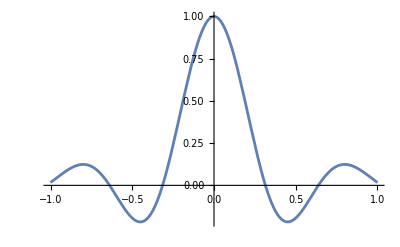

```mathematica
Plot[Evaluate[ ϕ[a]/.solution]/.{kt->10,mt->1},{a,-1,1},PlotRange->All]
```